# My Notebook

#### First Trial

Comments can be input here.

```mathematica
Options[InputNotebook[]]
```

{FrontEndVersion→12.1 for Microsoft Windows (64-bit) (June 19, 2020),InputAutoReplacements→{},StyleDefinitions→Default.nb,WindowMargins→{{Automatic,-5.4},{-5.4,Automatic}},WindowSize→{1152.,585.6},Magnification:>1.25 Inherited}

```mathematica
SetOptions[InputNotebook[],InputAutoReplacements->If[False,{"["->"[■]","{"->"{■}","("->"(■)"},{}]]
```

Comments are notes from now on.

```mathematica
If[True,Print[1]]
```

1

```mathematica
n=30
```

30

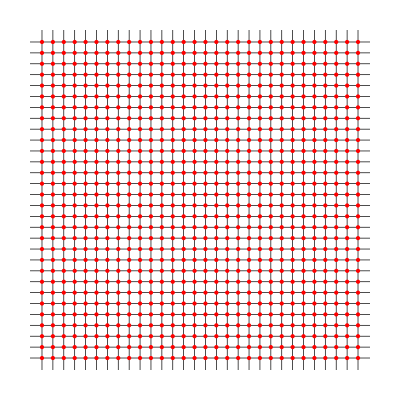

-Graphics-

grid_30.png

```mathematica
g= Graphics[{Table[{Red,Point[{i,j}]}, {i, 0.5, n-.5, 1},{j, 0.5, n-.5, 1}]},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@If[True,NotebookDirectory[],SystemDialogInput["Directory"]];
Export[StringTemplate["grid_``.png"][n],img]
```

#### Second Trial

20

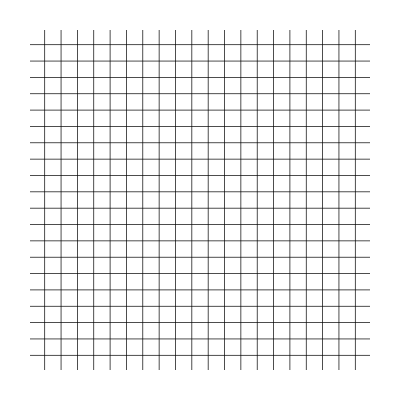

-Graphics-

grid_20.png

```mathematica
n=20
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["grid_``.png"][n],img]
```

50

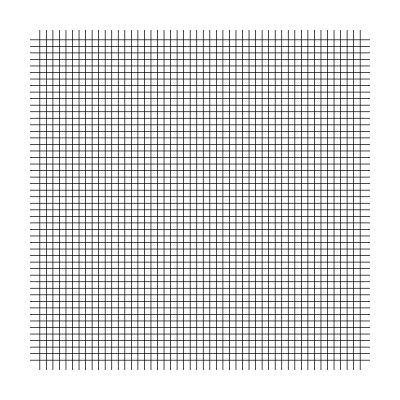

-Graphics-

grid_50.png

```mathematica
n=50
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["grid_``.png"][n],img]
```

40

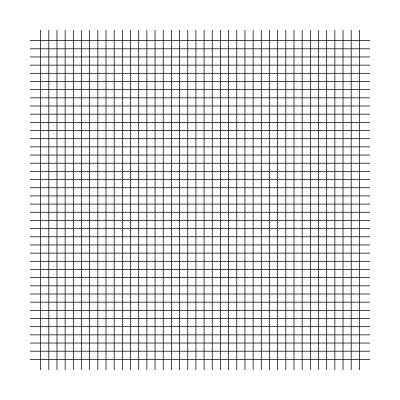

-Graphics-

grid_40.png

```mathematica
n=40
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["grid_``.png"][n],img]
```

10

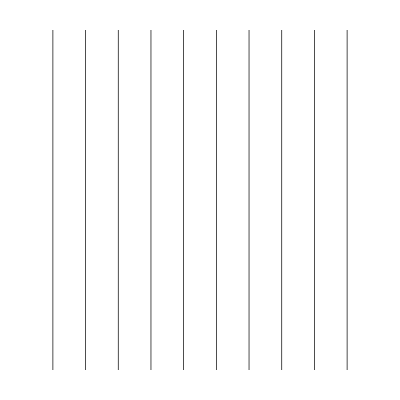

-Graphics-

vertical_10.png

```mathematica
n=10
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
{}}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["vertical_``.png"][n],img]
```

20

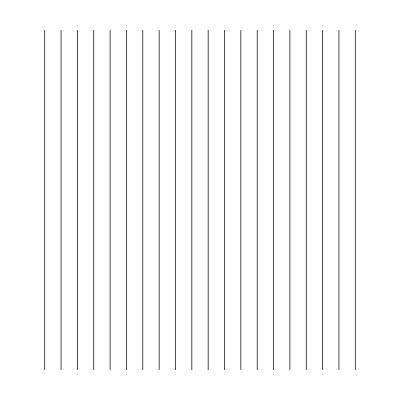

-Graphics-

vertical_20.png

```mathematica
n=20
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
{}}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["vertical_``.png"][n],img]
```

30

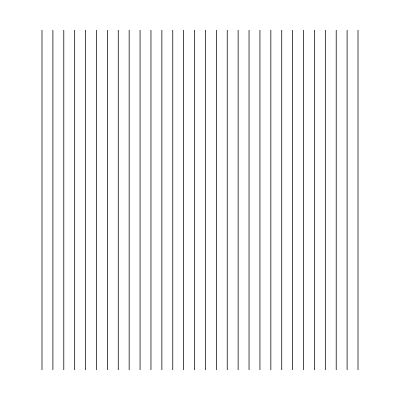

-Graphics-

vertical_30.png

```mathematica
n=30
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
{}}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["vertical_``.png"][n],img]
```

40

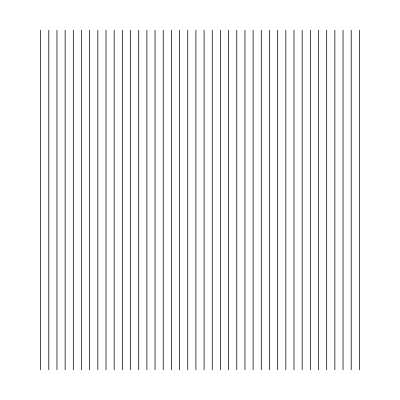

-Graphics-

vertical_40.png

```mathematica
n=40
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
{}}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["vertical_``.png"][n],img]
```

```mathematica
Import["vertical_40.png"]
```

-Graphics-

50

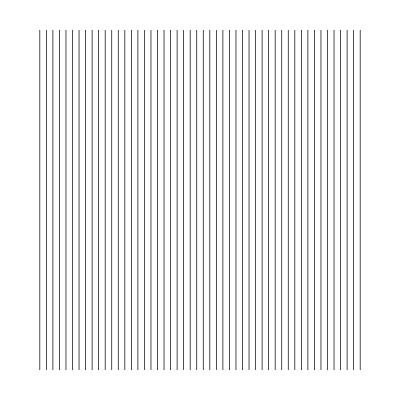

-Graphics-

vertical_50.png

```mathematica
n=50
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}],
{}}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["vertical_``.png"][n],img]
```

50

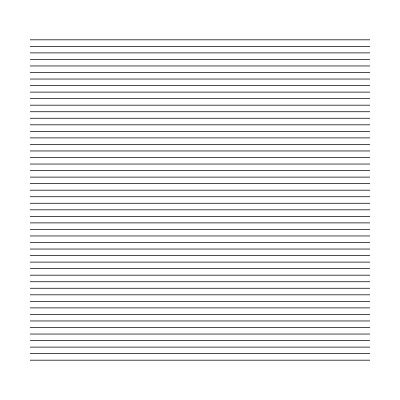

-Graphics-

horizontal_50.png

```mathematica
n=50
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {{},
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["horizontal_``.png"][n],img]
```

40

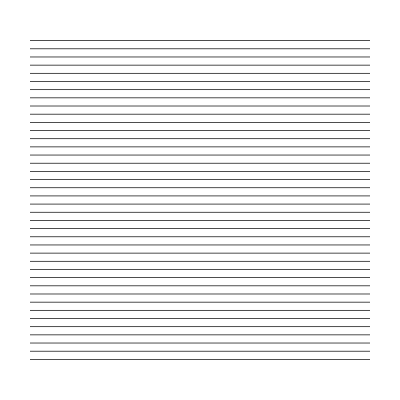

-Graphics-

horizontal_40.png

```mathematica
n=40
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {{},
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["horizontal_``.png"][n],img]
```

30

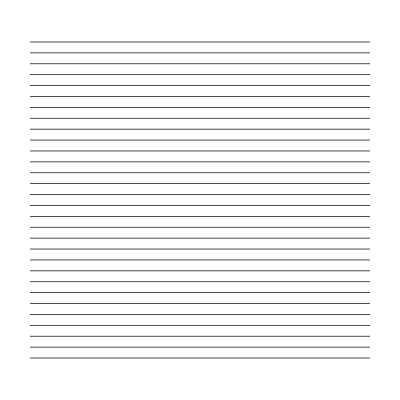

-Graphics-

horizontal_30.png

```mathematica
n=30
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {{},
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["horizontal_``.png"][n],img]
```

20

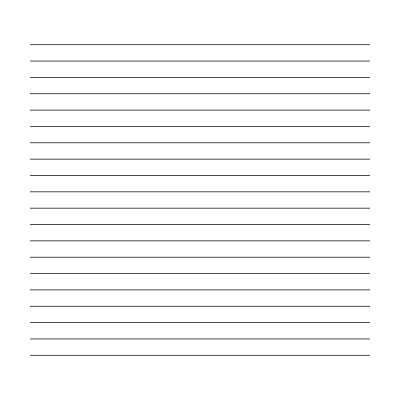

-Graphics-

horizontal_20.png

```mathematica
n=20
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {{},
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["horizontal_``.png"][n],img]
```

10

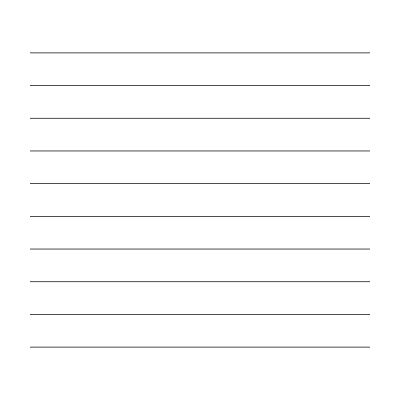

-Graphics-

horizontal_10.png

```mathematica
n=10
g= Graphics[{},PlotRange-> {{0,n},{0,n} },
GridLines-> {{},
Table[{i, RGBColor[0,0,0]}, {i, 0.5, n-.5, 1}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["horizontal_``.png"][n],img]
```

50

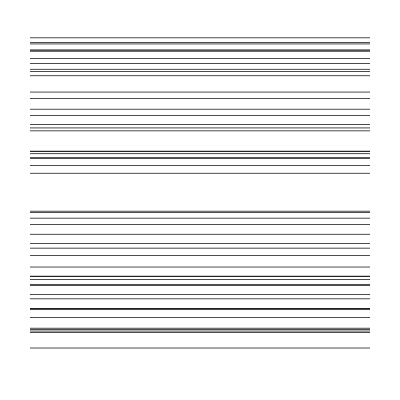

-Graphics-

randhor_50.png

```mathematica
n=50
g= Graphics[{},PlotRange-> {{0,1},{0,1} },
GridLines-> {{},
Table[{RandomReal[], RGBColor[0,0,0]}, {n}]}]
img=Image[g,ImageSize->250,ImageResolution->Automatic]
SetDirectory@NotebookDirectory[];
Export[StringTemplate["randhor_``.png"][n],img]
```